# B_c Mixing Angle: Momentum-Space QCD Sum Rule

Thin wrapper around BcMixingMomentum.wl. Evaluate from top to bottom in a Wolfram kernel where FeynCalc is installed. This notebook intentionally stores input cells only, so Mathematica does not save fragile evaluated Dataset boxes.

## Load

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
Get["BcMixingMomentum_claude.wl"];
```

FeynCalc 10.2.0 (stable version). For help, use the online documentation, visit the forum and have a look at the supplied examples. The PDF-version of the manual can be downloaded here.

If you use FeynCalc in your research, please evaluate FeynCalcHowToCite[] to learn how to cite this software.

Please keep in mind that the proper academic attribution of our work is crucial to ensure the future development of this package!

Loaded BcMixingMomentum.wl.  Run CheckEnvironment[] for setup information.

```mathematica
CheckEnvironment[]
```

<|FeynCalcLoaded→True,FeynCalcVersion→10.2.0,TensorCurrentKeepsRawI→True,TensorCurrentScale→mb+mc,Nc→3,Threshold→(mb+mc)^2,DefaultParameters→<|mb→4.18,mc→1.27,G2→0.473741,G3→0.57,alphaS→0.26,M2→10.,s0→55.|>,DefaultUncertaintyRanges→<|mb→{4.16,4.21},mc→{1.25,1.29},G2→{0.236871,0.710612},G3→{0.28,0.86},M2→{8.,12.},s0→{50.,60.}|>,MonteCarloIncludeG3→False|>

## Run Settings

```mathematica
m2Test = 8.0;
s0Test = 53.0;
stabilityOrder = "total";
stabilityNPoints = 25;
stabilityYHalfWidth = 1.0;
stabilityUseMaTeX = True;
stabilityExportPDF = True;
monteCarloSamples = 50;
monteCarloBins = 15;
monteCarloIncludeG3 = True;
requestCompleteD6CrossLineMonteCarlo = False;
showCachedCompleteD6CentralQuote = False;
completeD6CrossLineCacheDirectory = "d6_chunks";
completeD6PlotS0 = 53.0;
completeD6GridNPoints = stabilityNPoints;
generateCompleteD6CrossLineM2Grid = True;
overwriteCompleteD6CrossLineM2Grid = False;
runCompleteD6CrossLineTest = False;
```

The default publication workflow uses total OPE: perturbative + G2 + the standard single-line dimension-6 G3 term. Complete-D6 cross-line terms are handled only in the explicit grid section below.

## Mass-Dimension Checks

```mathematica
MixingMassDimensionReport[]
```

<|AA→<|CurrentDimensions→{3,3},CorrelatorDimension→2,SpectralDensityDimension→2,BorelMomentDimensionInThisConvention→4|>,AB→<|CurrentDimensions→{3,3},CorrelatorDimension→2,SpectralDensityDimension→2,BorelMomentDimensionInThisConvention→4|>,BA→<|CurrentDimensions→{3,3},CorrelatorDimension→2,SpectralDensityDimension→2,BorelMomentDimensionInThisConvention→4|>,BB→<|CurrentDimensions→{3,3},CorrelatorDimension→2,SpectralDensityDimension→2,BorelMomentDimensionInThisConvention→4|>|>

```mathematica
CheckMixingMassDimensions[]
```

True

```mathematica
PerturbativeSpectralDensityDimensionReport[]
```

<|AA→<|Name→rhoPertAA,Dimension→2,Expected→2,Pass→True|>,AB→<|Name→rhoPertAB,Dimension→2,Expected→2,Pass→True|>,BA→<|Name→rhoPertBA,Dimension→2,Expected→2,Pass→True|>,BB→<|Name→rhoPertBB,Dimension→2,Expected→2,Pass→True|>|>

## Central Values

```mathematica
NumericOPESummary[m2Test, s0Test] // Dataset
```

```mathematica
Association[
  "thetaPertDeg" -> NumericMixingAngleDegrees[m2Test, s0Test, "pert"],
  "thetaPertG2Deg" -> NumericMixingAngleDegrees[m2Test, s0Test, "pertG2"],
  "thetaTotalDeg" -> NumericMixingAngleDegrees[m2Test, s0Test, "total"]
] // Dataset
```

## Complete Dimension-6 Central Check

This is a numerical audit table only. For publication, use the theta-vs-M2 line plots below, not a bar chart at one point.

```mathematica
Get["BcMixingDimension6Complete.wl"];
```

Loaded BcMixingDimension6Complete.wl. Run D6CompletenessReport[] for the missing cross-line sector.

```mathematica
completeD6CentralSummary = D6CrossLineCentralSummary[completeD6CrossLineCacheDirectory];
completeD6CentralSummary // Dataset
```

```mathematica
completeD6CentralShift = D6CrossLineCentralAngleShift[
  8.0,
  54.0,
  $BcMixingDefaultParameters,
  completeD6CrossLineCacheDirectory
];
completeD6CentralShift // Dataset
```

```mathematica
centralThetaComparison = <|
  "pert" -> NumericMixingAngleDegrees[8.0, 54.0, "pert"],
  "pert + G2" -> NumericMixingAngleDegrees[8.0, 54.0, "pertG2"],
  "pert + G2 + G3 single-line" -> NumericMixingAngleDegrees[8.0, 54.0, "total"],
  "pert + G2 + G3 single-line + G3 cross-line" -> If[
    AssociationQ[completeD6CentralShift],
    completeD6CentralShift["ThetaWithCrossLineDeg"],
    Missing["NoCrossLineCache"]
  ]
|>;
centralThetaComparison // Dataset
```

```mathematica
completeD6MomentRatioTable = If[
  AssociationQ[completeD6CentralShift],
  AssociationMap[
    <|
      "G3CrossLineMoment" -> completeD6CentralShift["CrossLineMoments"][#],
      "G3CrossLineOverTotal" -> completeD6CentralShift["CrossLineOverBase"][#]
    |> &,
    {"AA", "AB", "BB"}
  ],
  completeD6CentralShift
];
completeD6MomentRatioTable // Dataset
```

```mathematica
If[
  TrueQ[showCachedCompleteD6CentralQuote] && AssociationQ[completeD6CentralShift],
  "Central complete-D6 angle = " <> ToString[NumberForm[completeD6CentralShift["ThetaWithCrossLineDeg"], {8, 6}]] <> " deg",
  "Central complete-D6 cross-line correction is displayed above but not inserted into scans. This is a cached central-point check, not an M2-s0 grid."
]
```

Central complete-D6 cross-line correction is displayed above but not inserted into scans. This is a cached central-point check, not an M2-s0 grid.

## Complete-D6 M2 Grid

This block is the slow but clean way to add the open-field cross-line dimension-6 correction to the theta-vs-M2 contribution plot. Leave generateCompleteD6CrossLineM2Grid = False to only load an existing cache. Set it to True when you are ready to compute the grid; each M2 point is cached in completeD6CrossLineCacheDirectory.

```mathematica
completeD6CrossLineM2Grid = If[
  TrueQ[generateCompleteD6CrossLineM2Grid],
  D6ComputeCrossLineM2Grid[
    $BcMixingWangWindow["M2Range"],
    completeD6PlotS0,
    $BcMixingDefaultParameters,
    "NPoints" -> completeD6GridNPoints,
    "CacheDirectory" -> completeD6CrossLineCacheDirectory,
    "Overwrite" -> overwriteCompleteD6CrossLineM2Grid,
    "Progress" -> True,
    WorkingPrecision -> MachinePrecision,
    AccuracyGoal -> 6,
    PrecisionGoal -> 6
  ],
  D6LoadCrossLineM2Grid[
    completeD6PlotS0,
    completeD6GridNPoints,
    completeD6CrossLineCacheDirectory
  ]
];
completeD6CrossLineM2Grid
```

Computing G3cross grid point M2 = 7., s0 = 53.

Computing G3cross grid point M2 = 7.08333, s0 = 53.

Computing G3cross grid point M2 = 7.16667, s0 = 53.

Computing G3cross grid point M2 = 7.25, s0 = 53.

Computing G3cross grid point M2 = 7.33333, s0 = 53.

Computing G3cross grid point M2 = 7.41667, s0 = 53.

Computing G3cross grid point M2 = 7.5, s0 = 53.

Computing G3cross grid point M2 = 7.58333, s0 = 53.

Computing G3cross grid point M2 = 7.66667, s0 = 53.

Computing G3cross grid point M2 = 7.75, s0 = 53.

Computing G3cross grid point M2 = 7.83333, s0 = 53.

Computing G3cross grid point M2 = 7.91667, s0 = 53.

Computing G3cross grid point M2 = 8., s0 = 53.

Computing G3cross grid point M2 = 8.08333, s0 = 53.

Computing G3cross grid point M2 = 8.16667, s0 = 53.

Computing G3cross grid point M2 = 8.25, s0 = 53.

Computing G3cross grid point M2 = 8.33333, s0 = 53.

Computing G3cross grid point M2 = 8.41667, s0 = 53.

Computing G3cross grid point M2 = 8.5, s0 = 53.

Computing G3cross grid point M2 = 8.58333, s0 = 53.

Computing G3cross grid point M2 = 8.66667, s0 = 53.

Computing G3cross grid point M2 = 8.75, s0 = 53.

Computing G3cross grid point M2 = 8.83333, s0 = 53.

Computing G3cross grid point M2 = 8.91667, s0 = 53.

Computing G3cross grid point M2 = 9., s0 = 53.

<|Type→D6CrossLineM2Grid,Order→G3cross,M2Range→{7.,9.},s0→53.,NPoints→25,M2Values→{7.,7.08333,7.16667,7.25,7.33333,7.41667,7.5,7.58333,7.66667,7.75,7.83333,7.91667,8.,8.08333,8.16667,8.25,8.33333,8.41667,8.5,8.58333,8.66667,8.75,8.83333,8.91667,9.},ParameterSnapshot→<|mb→4.18,mc→1.27,G2→0.473741,G3→0.57,alphaS→0.26,M2→10.,s0→55.|>,Records→{7.→<|AA→-9.51418×10^-7,AB→5.93791×10^-7,BB→Failure[…]|>,7.08333→<|AA→-9.83792×10^-7,AB→6.13291×10^-7,BB→Failure[…]|>,7.16667→<|AA→-1.01619×10^-6,AB→6.32689×10^-7,BB→Failure[…]|>,7.25→<|AA→-1.04858×10^-6,AB→6.51961×10^-7,BB→Failure[…]|>,7.33333→<|AA→-1.08093×10^-6,AB→6.71083×10^-7,BB→Failure[…]|>,7.41667→<|AA→-1.11323×10^-6,AB→6.90035×10^-7,BB→Failure[…]|>,7.5→<|AA→-1.14544×10^-6,AB→7.08794×10^-7,BB→Failure[…]|>,7.58333→<|AA→-1.17754×10^-6,AB→7.2734×10^-7,BB→Failure[…]|>,7.66667→<|AA→-1.20952×10^-6,AB→7.45655×10^-7,BB→Failure[…]|>,7.75→<|AA→-1.24133×10^-6,AB→7.63718×10^-7,BB→Failure[…]|>,7.83333→<|AA→-1.27298×10^-6,AB→7.81512×10^-7,BB→Failure[…]|>,7.91667→<|AA→-1.30443×10^-6,AB→7.9902×10^-7,BB→Failure[…]|>,8.→<|AA→-1.33566×10^-6,AB→8.16226×10^-7,BB→Failure[…]|>,8.08333→<|AA→-1.36667×10^-6,AB→8.33114×10^-7,BB→Failure[…]|>,8.16667→<|AA→-1.39743×10^-6,AB→8.49671×10^-7,BB→Failure[…]|>,8.25→<|AA→-1.42792×10^-6,AB→8.65881×10^-7,BB→Failure[…]|>,8.33333→<|AA→-1.45813×10^-6,AB→8.81733×10^-7,BB→Failure[…]|>,8.41667→<|AA→-1.48805×10^-6,AB→8.97214×10^-7,BB→Failure[…]|>,8.5→<|AA→-1.51765×10^-6,AB→9.12314×10^-7,BB→Failure[…]|>,8.58333→<|AA→-1.54694×10^-6,AB→9.2702×10^-7,BB→Failure[…]|>,8.66667→<|AA→-1.5759×10^-6,AB→9.41324×10^-7,BB→Failure[…]|>,8.75→<|AA→-1.60451×10^-6,AB→9.55217×10^-7,BB→Failure[…]|>,8.83333→<|AA→-1.63277×10^-6,AB→9.6869×10^-7,BB→Failure[…]|>,8.91667→<|AA→-1.66067×10^-6,AB→9.81737×10^-7,BB→Failure[…]|>,9.→<|AA→-1.68819×10^-6,AB→9.94348×10^-7,BB→Failure[…]|>},UpdatedAt→2026-06-14 15:28:43|>

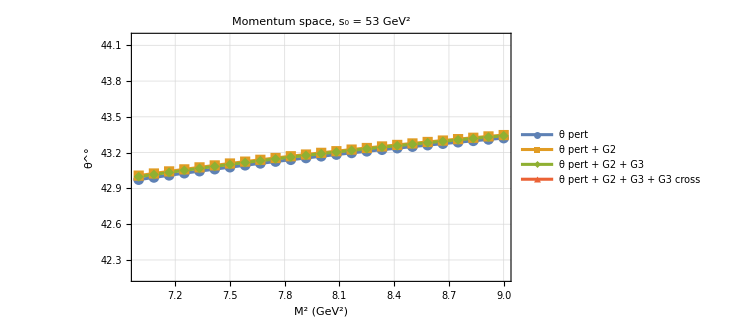
<|Data→<|pert→(7. | 42.9737
7.08333 | 42.9921
7.16667 | 43.0101
7.25 | 43.0277
7.33333 | 43.0449
7.41667 | 43.0617
7.5 | 43.0781
7.58333 | 43.0942
7.66667 | 43.11
7.75 | 43.1254
7.83333 | 43.1405
7.91667 | 43.1552
8. | 43.1697
8.08333 | 43.1839
8.16667 | 43.1977
8.25 | 43.2113
8.33333 | 43.2246
8.41667 | 43.2377
8.5 | 43.2505
8.58333 | 43.263
8.66667 | 43.2753
8.75 | 43.2873
8.83333 | 43.2992
8.91667 | 43.3108
9. | 43.3221),pertG2→(7. | 43.0073
7.08333 | 43.0252
7.16667 | 43.0427
7.25 | 43.0598
7.33333 | 43.0766
7.41667 | 43.093
7.5 | 43.109
7.58333 | 43.1247
7.66667 | 43.14
7.75 | 43.155
7.83333 | 43.1698
7.91667 | 43.1842
8. | 43.1983
8.08333 | 43.2121
8.16667 | 43.2257
8.25 | 43.2389
8.33333 | 43.2519
8.41667 | 43.2647
8.5 | 43.2772
8.58333 | 43.2894
8.66667 | 43.3015
8.75 | 43.3132
8.83333 | 43.3248
8.91667 | 43.3361
9. | 43.3473),total→(7. | 42.9981
7.08333 | 43.0162
7.16667 | 43.0339
7.25 | 43.0512
7.33333 | 43.0681
7.41667 | 43.0847
7.5 | 43.1009
7.58333 | 43.1167
7.66667 | 43.1322
7.75 | 43.1474
7.83333 | 43.1623
7.91667 | 43.1768
8. | 43.1911
8.08333 | 43.205
8.16667 | 43.2187
8.25 | 43.2321
8.33333 | 43.2452
8.41667 | 43.2581
8.5 | 43.2707
8.58333 | 43.2831
8.66667 | 43.2952
8.75 | 43.3071
8.83333 | 43.3187
8.91667 | 43.3302
9. | 43.3414),totalCompleteD6→(7. | —
7.08333 | —
7.16667 | —
7.25 | —
7.33333 | —
7.41667 | —
7.5 | —
7.58333 | —
7.66667 | —
7.75 | —
7.83333 | —
7.91667 | —
8. | —
8.08333 | —
8.16667 | —
8.25 | —
8.33333 | —
8.41667 | —
8.5 | —
8.58333 | —
8.66667 | —
8.75 | —
8.83333 | —
8.91667 | —
9. | —)|>,Plot→-Graphics-|>

```mathematica
completeD6ThetaOrderM2 = If[
  AssociationQ[completeD6CrossLineM2Grid],
  D6CompleteThetaOrderM2PublicationPlotFromGrid[
    completeD6CrossLineM2Grid,
    $BcMixingDefaultParameters,
    "YHalfWidth" -> stabilityYHalfWidth,
    "UseMaTeX" -> stabilityUseMaTeX
  ],
  completeD6CrossLineM2Grid
];
completeD6ThetaOrderM2
```

```mathematica
If[
  AssociationQ[completeD6ThetaOrderM2] && KeyExistsQ[completeD6ThetaOrderM2, "Plot"],
  completeD6ThetaOrderM2["Plot"],
  "No complete-D6 M2 grid plot yet. Set generateCompleteD6CrossLineM2Grid = True to compute and cache it."
]
```

-Graphics-

```mathematica
If[
  AssociationQ[completeD6ThetaOrderM2] && KeyExistsQ[completeD6ThetaOrderM2, "Data"],
  completeD6ThetaOrderM2["Data"] // Dataset,
  "No complete-D6 M2 grid data yet."
]
```

```mathematica
If[TrueQ[stabilityExportPDF] && AssociationQ[completeD6ThetaOrderM2] && KeyExistsQ[completeD6ThetaOrderM2, "Plot"],
  Export["BcMixingMomentumThetaOrdersCompleteD6VsM2_s0_53.pdf", completeD6ThetaOrderM2["Plot"]],
  "Complete-D6 theta-order PDF export skipped."
]
```

BcMixingMomentumThetaOrdersCompleteD6VsM2_s0_53.pdf

## OPE Hierarchy

```mathematica
OPEConvergenceDataset[{8.0, 12.0, 1.0}, {50.0, 60.0, 5.0}]
```

## Theta Decomposition at Fixed s0

This is the paper-facing comparison: the physical mixing angle is plotted for perturbative, perturbative plus G2, and total OPE orders at fixed s0. Here total means pert + G2 + the standard single-line dimension-6 G3 term.

```mathematica
thetaOrderM2 = MixingAngleOrderM2PublicationPlot[
  $BcMixingWangWindow["M2Range"],
  53.0,
  {"pert", "pertG2", "total"},
  $BcMixingDefaultParameters,
  "NPoints" -> stabilityNPoints,
  "YHalfWidth" -> stabilityYHalfWidth,
  "UseMaTeX" -> stabilityUseMaTeX
];
```

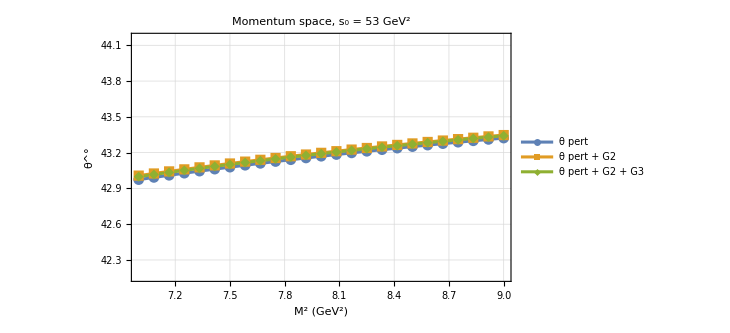

```mathematica
thetaOrderM2["Plot"]
```

```mathematica
thetaOrderM2["Data"] // Dataset
```

```mathematica
If[TrueQ[stabilityExportPDF],
  Export["BcMixingMomentumThetaOrdersVsM2_s0_53.pdf", thetaOrderM2["Plot"]],
  "Theta-order PDF export skipped. Set stabilityExportPDF = True when ready."
]
```

BcMixingMomentumThetaOrdersVsM2_s0_53.pdf

## OPE Ratio Diagnostics

This diagnostic plot is for OPE convergence, not for the final angle itself. It shows the channel-level sizes of G2 and G3 relative to the perturbative moment for AA, AB, and BB.

```mathematica
momentumRatioM2 = OPEContributionRatioM2PublicationPlot[
  $BcMixingWangWindow["M2Range"],
  53.0,
  $BcMixingDefaultParameters,
  "NPoints" -> stabilityNPoints,
  "UseAbs" -> True
];
```

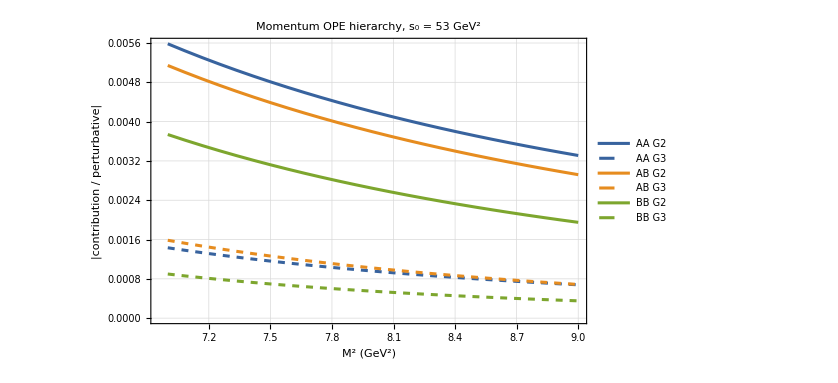

```mathematica
momentumRatioM2["Plot"]
```

```mathematica
momentumRatioM2["Data"] // Dataset
```

```mathematica
If[TrueQ[stabilityExportPDF],
  Export["BcMixingMomentumOPERatiosVsM2_s0_53.pdf", momentumRatioM2["Plot"]],
  "OPE-ratio PDF export skipped. Set stabilityExportPDF = True when ready."
]
```

BcMixingMomentumOPERatiosVsM2_s0_53.pdf

## Auxiliary-Parameter Stability

```mathematica
m2Stability = MixingAngleStabilityM2PublicationPlot[
  $BcMixingWangWindow["M2Range"],
  $BcMixingWangWindow["s0Values"],
  stabilityOrder,
  $BcMixingDefaultParameters,
  "NPoints" -> stabilityNPoints,
  "YHalfWidth" -> stabilityYHalfWidth,
  "UseMaTeX" -> stabilityUseMaTeX
];
```

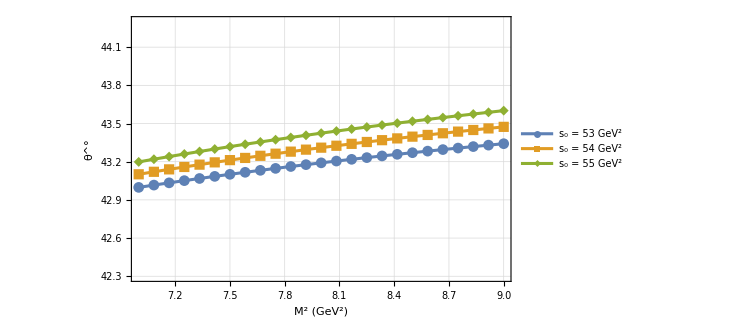

```mathematica
m2Stability["Plot"]
```

```mathematica
m2Stability["Data"] // Dataset
```

```mathematica
s0Stability = MixingAngleStabilityS0PublicationPlot[
  $BcMixingWangWindow["s0Range"],
  $BcMixingWangWindow["M2Values"],
  stabilityOrder,
  $BcMixingDefaultParameters,
  "NPoints" -> stabilityNPoints,
  "YHalfWidth" -> stabilityYHalfWidth,
  "UseMaTeX" -> stabilityUseMaTeX
];
```

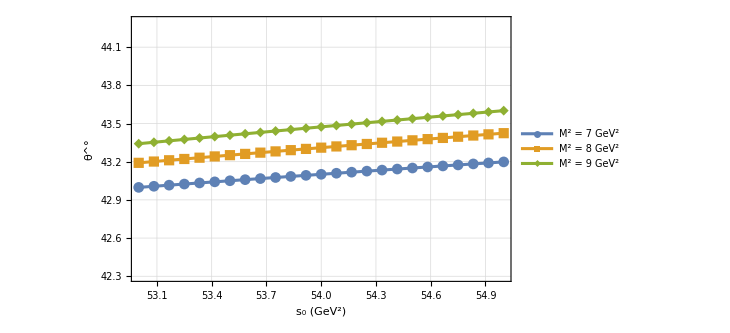

```mathematica
s0Stability["Plot"]
```

```mathematica
s0Stability["Data"] // Dataset
```

```mathematica
If[TrueQ[stabilityExportPDF],
  Export["BcMixingThetaVsM2_WangWindow.pdf", m2Stability["Plot"]];
  Export["BcMixingThetaVsS0_WangWindow.pdf", s0Stability["Plot"]];
  "Stability PDFs exported.",
  "Stability PDF export skipped. Set stabilityExportPDF = True when ready."
]
```

Stability PDFs exported.

```mathematica
ExportStabilityDataCSV[m2Stability["Data"], "BcMixingThetaVsM2_WangWindow.csv", "M2"];
ExportStabilityDataCSV[s0Stability["Data"], "BcMixingThetaVsS0_WangWindow.csv", "s0"];
```

## Monte Carlo Uncertainty

```mathematica
If[TrueQ[requestCompleteD6CrossLineMonteCarlo],
  "Complete-D6 cross-line Monte Carlo is NOT available from the central or M2-only cache. Generate a full M2-s0-parameter grid/interpolation first. This run remains production total: pert + G2 + single-line G3.",
  "Monte Carlo uses production total: pert + G2 + single-line G3. Cached complete-D6 cross-line corrections are not sampled in this uncertainty run."
]
```

Monte Carlo uses production total: pert + G2 + single-line G3. Cached complete-D6 cross-line corrections are not sampled in this uncertainty run.

```mathematica
uncertaintyRanges = Join[
  $BcMixingDefaultUncertaintyRanges,
  <|
    "M2" -> $BcMixingWangWindow["M2Range"],
    "s0" -> $BcMixingWangWindow["s0Range"]
  |>
];
```

```mathematica
uncertaintyRanges // Dataset
```

```mathematica
uncertaintyRun = MonteCarloMixingAngleUncertainty[
  monteCarloSamples,
  uncertaintyRanges,
  "total",
  "IncludeG3" -> monteCarloIncludeG3,
  "Seed" -> 1234,
  "Progress" -> True
];
```

Monte Carlo sample 5/50

Monte Carlo sample 10/50

Monte Carlo sample 15/50

Monte Carlo sample 20/50

Monte Carlo sample 25/50

Monte Carlo sample 30/50

Monte Carlo sample 35/50

Monte Carlo sample 40/50

Monte Carlo sample 45/50

Monte Carlo sample 50/50

```mathematica
uncertaintyRun["Summary"] // Dataset
```

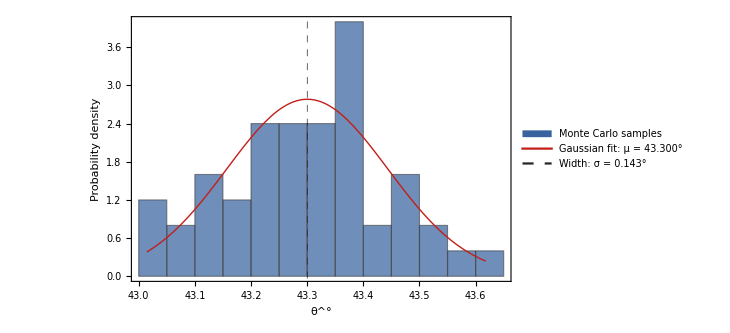

```mathematica
MonteCarloMixingAnglePublicationHistogram[uncertaintyRun, monteCarloBins]
```

```mathematica
ExportMonteCarloMixingAngleSamples[uncertaintyRun, "BcMixingMonteCarloSamples.csv"];
ExportMonteCarloMixingAngleSummary[uncertaintyRun, "BcMixingMonteCarloSummary.csv"];
```

## Complete Dimension-6 Audit

This audit keeps the derivation status visible. The cached complete-D6 central values and optional M2 grid are handled above.

```mathematica
D6CompletenessReport[] // Dataset
```

```mathematica
D6CrossLineValidationStatus[] // Dataset
```

```mathematica
D6CompletionChecklist[] // Column
```

Fix the exact open two-gluon heavy-quark propagator S_Q^(GG,open) in the same convention as SGNum.
Check the triple-gluon vacuum tensor normalization and sign against the definition of <g_s^3 G^3> used in the paper.
Build the two cross-line kernels S_c^(GG)S_b^(G) and S_c^(G)S_b^(GG) for AA, AB and BB.
Reduce the kernels to scalar Feynman-parameter amplitudes.
Convert amplitudes into direct Borel pole weights and test reconstruction against the amplitude.
Only after these checks, define G3complete = G3c + G3b + G3cross and totalComplete = pert + G2full + G3complete.

```mathematica
If[TrueQ[runCompleteD6CrossLineTest],
  D6NumericBorelPiCrossLine[
    "AA", 8.0, 54.0, $BcMixingDefaultParameters, "c2b1",
    WorkingPrecision -> MachinePrecision,
    AccuracyGoal -> 6,
    PrecisionGoal -> 6
  ],
  "Complete dimension-6 cross-line test skipped. Set runCompleteD6CrossLineTest = True to run it."
]
```

Complete dimension-6 cross-line test skipped. Set runCompleteD6CrossLineTest = True to run it.

## G3 Caveat

The default total result includes the standard vacuum-averaged single-line contribution S_c^(G3) S_b^0 + S_c^0 S_b^(G3). The optional totalCompleteD6 curve adds the cached open-field cross-line G3 pieces on an M2 grid.